```mathematica
mudis=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-mu-dis-microBoone-no.dat","Data"];
```

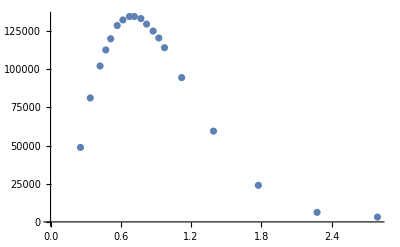

```mathematica
ListPlot[mudis]
```

```mathematica
Sum[mudis[[i,2]]*murate[[i,2]],{i,1,Length[murate]}]
```

142556.

```mathematica
murate=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/sig-bg-SBND/micro-m-sig.dat","Data"];
```

```mathematica
Table[((mudis[[i,2]]*murate[[i,2]])/(murate[[i,3]])),{i,1,Length[mudis]}]
```

{0.0629852,0.0479392,0.0413781,0.0376462,0.0342948,0.0322838,0.0296804,0.0274722,0.0255483,0.0240895,0.022731,0.0215299,0.0205758,0.0195151,0.0172457,0.0141664,0.0133488,0.0176696,0.0209086}

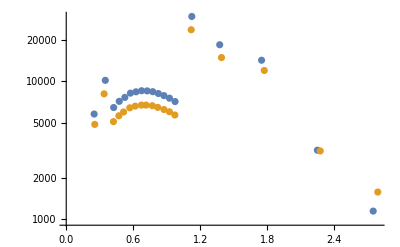

```mathematica
ListLogPlot[{Table[{murate[[i,1]],murate[[i,3]]},{i,1,Length[murate]}],Table[{mudis[[i,1]],mudis[[i,2]]*murate[[i,2]]},{i,1,Length[murate]}]}]
```

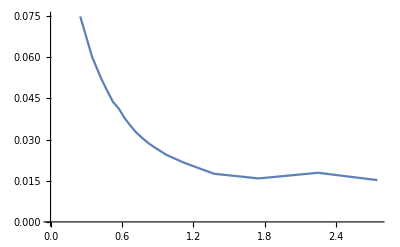

```mathematica
ListPlot[Table[{murate[[i,1]],(mudis[[i,2]]*murate[[i,2]])/(murate[[i,3]])},{i,1,Length[mudis]}],Joined->True]
```

```mathematica
murate2=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBN/ev-rat-nu-mu.dat","Data"];
```

```mathematica
murate
```

{{0.25,0.1,144828,0},{0.35,0.1,302569,0},{0.425,0.05,212305,0},{0.475,0.05,254988,0},{0.525,0.05,297000,0},{0.575,0.05,338569,0},{0.625,0.05,379659,0},{0.675,0.05,417456,0},{0.725,0.05,448730,0},{0.775,0.05,473076,0},{0.825,0.05,491511,0},{0.875,0.05,503980,0},{0.925,0.05,510622,0},{0.975,0.05,511765,0},{1.125,0.25,2.39711×10^6,0},{1.375,0.25,1.80641×10^6,0},{1.75,0.5,1.53437×10^6,0},{2.25,0.5,339281,0},{2.75,0.5,145625,0}}

```mathematica
Table[{murate2[[i,1]],(murate2[[i,3]]/murate2[[i,2]])},{i,1,Length[murate2]}]
```

{{0.25,83290.7},{0.35,137789.},{0.425,176864.},{0.475,193316.},{0.525,212854.},{0.575,225194.},{0.625,234448.},{0.675,239588.},{0.725,241646.},{0.775,245758.},{0.825,235476.},{0.875,230334.},{0.925,224164.},{0.975,212854.},{1.125,175835.},{1.375,108997.},{1.75,42159.4},{2.25,10282.8},{2.75,4113.12}}

```mathematica
mudis
```

```mathematica
murate3=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBN/ev-rat-nu-mu.dat","Data"];
```

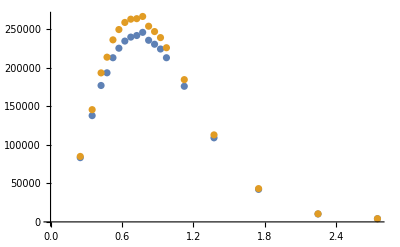

```mathematica
ListPlot[{Table[{murate2[[i,1]],murate2[[i,3]]/murate2[[i,2]]},{i,1,Length[murate2]}],Table[{murate3[[i,1]],murate3[[i,3]]/murate3[[i,2]]},{i,1,Length[murate3]}]}]
```

```mathematica
eapp=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-sig-MICRO.dat","Data"];
```

```mathematica
eappc=Table[{eapp[[i,1]],(eapp[[i+1,2]]-eapp[[i,2]])},{i,1,Length[eapp],2}];
```

```mathematica
eappc
```

{{0.279857,155.077},{0.424599,215.385},{0.574332,172.308},{0.729055,129.223},{0.878788,86.1538},{1.02353,56.},{1.20321,34.4539},{1.39786,17.2308},{1.62246,12.9231},{1.87701,8.61538},{2.50089,0.}}

```mathematica
erate=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/mb-me-ev.dat","Data"];
```

```mathematica
erate
```

{{0.275,0.15,149575,146780},{0.425,0.15,370314,362166},{0.575,0.15,596973,582879},{0.725,0.15,784844,765561},{0.875,0.15,868197,846600},{1.025,0.15,865665,844136},{1.2,0.2,1.03902×10^6,1.01349×10^6},{1.4,0.2,807392,788339},{1.625,0.25,612576,599872},{1.875,0.25,285093,281155},{2.5,1,252849,255369}}

```mathematica
Length[eappc]
```

11

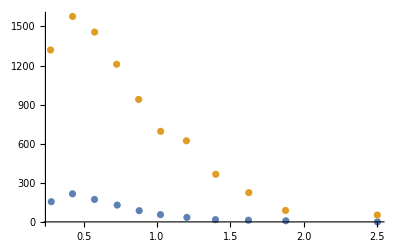

```mathematica
ListPlot[{eappc,Table[{erate[[i,1]],erate[[i,3]]},{i,1,Length[erate]}]},PlotRange->All]
```

```mathematica
Table[((eappc[[i,2]]*erate[[i,2]])/(erate[[i,3]])),{i,1,Length[eappc]}]
```

{0.0176317,0.0204941,0.0177459,0.0160216,0.0137517,0.0120872,0.0110718,0.00942904,0.0143968,0.02458,0.}

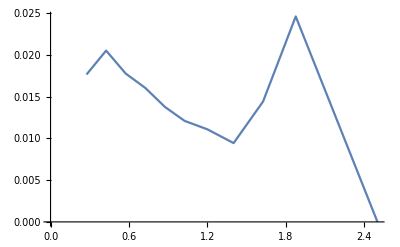

```mathematica
ListPlot[Table[{erate[[i,1]],(eappc[[i,2]]*erate[[i,2]])/(erate[[i,3]])},{i,1,Length[eappc]}],Joined->True]
```

```mathematica
ebg=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-bg-MICRO.dat","Data"];
```

```mathematica
ebg
```

{{0.274866,423.077},{0.434581,826.923},{0.574332,1000},{0.734046,961.538},{0.878788,942.308},{1.02353,865.385},{1.19822,769.231},{1.40285,615.385},{1.62246,509.615},{1.87701,403.846},{2.50588,192.308}}

```mathematica
eratebg=Import["/home/gstenico/Downloads/GLOBES/globes-3.2.17/SBND/mb-me-bg2.dat","Data"];
```

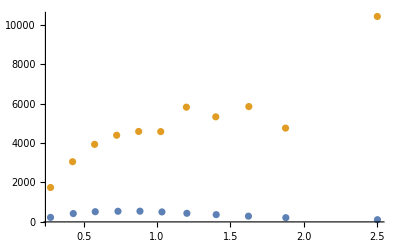

```mathematica
ListPlot[{ebg,Table[{eratebg[[i,1]],eratebg[[i,3]]},{i,1,Length[eratebg]}]},PlotRange->All]
```

```mathematica
Table[((ebg[[i,2]]*eratebg[[i,2]])/(eratebg[[i,3]])),{i,1,Length[ebg]}]
```

{0.0196347,0.0207609,0.019736,0.0184081,0.0177845,0.0165526,0.0150089,0.0138126,0.0124301,0.0112286,0.0106771}

```mathematica
ebg2=Import["/home/gstenico/Desktop/nu-LED-2/ev-rates/nu-e-app-bg2-MICRO.dat","Data"];
ebg2c=Table[{ebg2[[i,1]],(ebg2[[i+1,2]]-ebg2[[i,2]])},{i,1,Length[ebg2],2}];
```

```mathematica
Length[ebg2c]
```

11

```mathematica
Table[((ebg2c[[i,2]]*eratebg[[i,2]])/(eratebg[[i,3]])),{i,1,Length[ebg2c]}]
```

{0.0000388794,0.0000174488,6.4943×10^-6,4.11792×10^-6,2.97832×10^-6,2.9857×10^-6,1.65837×10^-6,1.06706×10^-6,3.51605×10^-6,7.55489×10^-6,0.}